# Sea-Ice Thermal Spin-Up: Vertical Temperature Profiles

Visualizes the reconstructed vertical temperature profile T(z) (see heat_equation_spec.md, formula (R)) for a sample of points printed to console by DataPreparer::ThermalSpinUpSave (preparer/data_preparer.cpp) after a thermal spin-up run. Each row below is one point: {A1, A2, A3, Ts_old, H}. Paste the latest printed line into the data list, then evaluate the whole notebook (Evaluation > Evaluate Notebook).

## Constants and reconstruction formula

```mathematica
Tb = -1.8; (* deg C, fixed ocean/bottom boundary temperature, see SimParams::T_bottom *)
T[z_, Ts_, A1_, A2_, A3_, H_] := Ts + (Tb - Ts) z/H + A1 Sin[Pi z/H] + A2 Sin[2 Pi z/H] + A3 Sin[3 Pi z/H];
```

## Sample data

```mathematica
(* Each row: {A1, A2, A3, Ts_old, thickness H}, printed by ThermalSpinUpSave *)
data = {{-0.627062,0.0536493,0.0672274,-0.563635,1.12249},{-2.18392,-0.687443,-0.307011,-0.190771,2.26634},{-1.48361,-0.261503,-0.0696807,-0.00281372,1.93188},{-2.97215,-0.93694,-0.252556,0.012262,1.71462},{-1.06757,-0.0440154,0.0415906,-0.88465,1.87907},{-3.19858,-1.25852,-0.490699,-0.97251,2.14298},{-0.606172,0.0570905,0.0500691,-0.792426,0.992328},{-3.42853,-1.11753,-0.515712,-0.00662842,2.64699},{-1.62957,-0.243458,-0.0597387,-0.110297,1.92241},{-1.19218,-0.152271,0.0256091,-0.76261,1.85453}};
(* NOTE: the thicknesses above are placeholders (1.0) -- the printed sample 
   this notebook was first built from predates adding H to the debug print. 
   Replace this whole list with the new {A1,A2,A3,Ts,H} output. *)
```

## Vertical profiles (depth 0 = surface, H = ocean boundary)

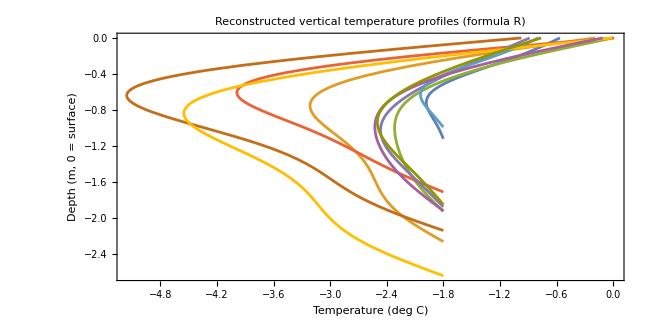

```mathematica
profiles = Table[
  With[{A1 = data[[i, 1]], A2 = data[[i, 2]], A3 = data[[i, 3]], Ts = data[[i, 4]], H = data[[i, 5]]},
    Legended[
      ParametricPlot[{T[z, Ts, A1, A2, A3, H], -z}, {z, 0, H}, PlotStyle -> ColorData[97][i]],
      "Point " <> ToString[i]
    ]
  ],
  {i, Length[data]}
];

Show[profiles, PlotRange -> All, Frame -> True,
 FrameLabel -> {"Temperature (deg C)", "Depth (m, 0 = surface)"},
 PlotLabel -> "Reconstructed vertical temperature profiles (formula R)",
 ImageSize -> 650]
```

## Surface vs. bottom temperature, per point

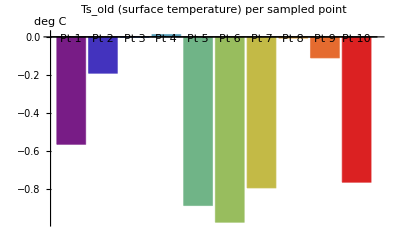

```mathematica
BarChart[data[[All, 4]], ChartLabels -> Table["Pt " <> ToString[i], {i, Length[data]}],
 PlotLabel -> "Ts_old (surface temperature) per sampled point",
 ChartStyle -> "Rainbow", AxesLabel -> {None, "deg C"}]
```